The aim is to learn how to integrate 2D peaks by marking a rectangle on the contour plot.

```mathematica
data= {{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0}
,{1,2,0},{2,2,5},{3,2,5},{4,2,5},{5,2,0}
, {1,3,0},{2,3,5},{3,3,10},{4,3,5},{5,3,0}
,{1,4,0},{2,4,5},{3,4,5},{4,4,5},{5,4,0}
,{1,5,0},{2,5,0},{3,5,0},{4,5,0},{5,5,0}
}
```

{{1,1,0},{2,1,0},{3,1,0},{4,1,0},{5,1,0},{1,2,0},{2,2,5},{3,2,5},{4,2,5},{5,2,0},{1,3,0},{2,3,5},{3,3,10},{4,3,5},{5,3,0},{1,4,0},{2,4,5},{3,4,5},{4,4,5},{5,4,0},{1,5,0},{2,5,0},{3,5,0},{4,5,0},{5,5,0}}

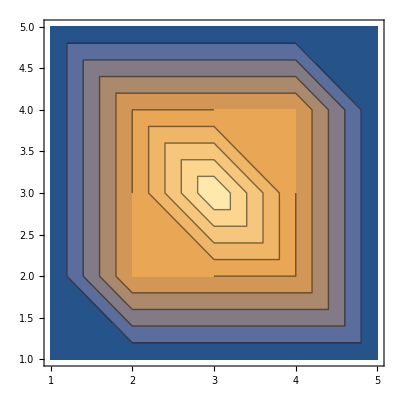

```mathematica
ListContourPlot[data]
```

```mathematica
ListPlot3D[data]
```

-Graphics3D-

```mathematica
contourplot =ListContourPlot[data]
```

-Graphics-

```mathematica
DynamicModule[{pt1={3,2}, pt2={4,4}}
,{LocatorPane[Dynamic[{pt1,pt2}], Show[contourplot,Epilog->{EdgeForm[{Thick,Red}],FaceForm[],Dynamic[Rectangle[pt1,pt2]]}]]
,xy1=Dynamic[pt1[[1]]]
,xy2=Dynamic[pt2[[1]]]
,Dynamic[select=Position[data,{x_/;(x≥pt1[[1]]&&x≤pt2[[1]]),y_ /; (y≥pt1[[2]]&&y≤pt2[[2]]),z_}]]
, Dynamic[Total[data[[Flatten[select]]]]]
}
]
```

```mathematica
Total[data[[Flatten[{{12},{13},{14},{17},{18},{19}}]]]]
```

{18,21,35}

```mathematica
Total[data
```

```mathematica
MatchQ[{x_ /;(x≥2),y_,z_}]/@data
```

{False,True,True,True,True,False,True,True,True,True,False,True,True,True,True,False,True,True,True,True,False,True,True,True,True}

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
DynamicModule[{pt1={2,2}, pt2={4,4}}
,{LocatorPane[Dynamic[{pt1,pt2}], ListContourPlot[data,Epilog->{EdgeForm[{Thick,Red}],FaceForm[],Rectangle[Dynamic[pt1],Dynamic[pt2]]}]]
,Dynamic[pt1[[1]]]
, Dynamic[pt2][[1]]
,Position[data,{x_/;(x≥ 2&&x≤4),y_,z_}]
}
]
```

```mathematica
Position[data,{x_/;(x≥ 2&&x≤ 4),y_,z_}]
```

{{2},{3},{4},{7},{8},{9},{12},{13},{14},{17},{18},{19},{22},{23},{24}}

```mathematica
DynamicModule[{pt1={2,2}}
,{LocatorPane[{Dynamic[pt1], }, ListContourPlot[data,Epilog->Line[{Dynamic[pt1],Dynamic[pt2]}]]]
,Dynamic[pt1], Dynamic[pt2]}
]
```

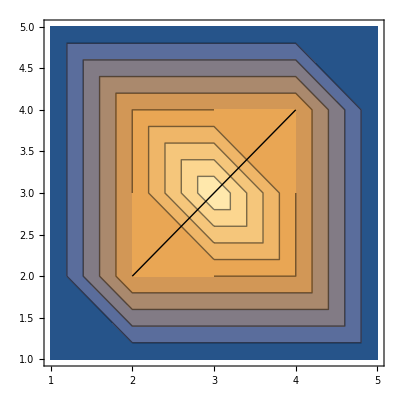

```mathematica
ListContourPlot[data, ]]
```

```mathematica
{1,2,3}===   {1,2,3.0}
```

False